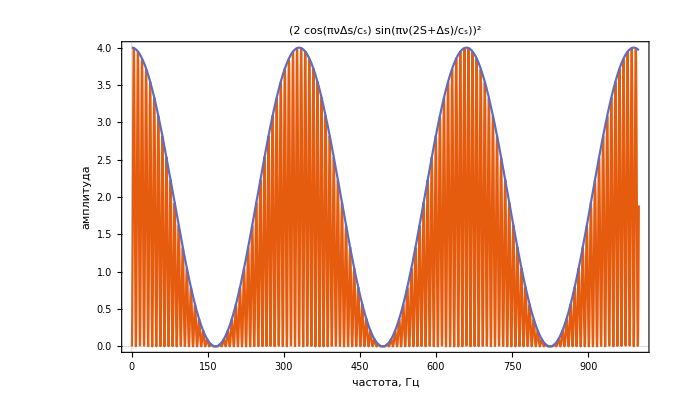

```mathematica
Plot[{
Evaluate[(2 Cos[(dx π)/(330/ν)] Sin[(π (dx+2 x1))/(330/ν)])^2/.{dx->1,x1->20}],
Evaluate[(2 Cos[(dx π)/(330/ν)] )^2/.{dx->1,x1->20}]
}
,{ν,0,1000},
PlotTheme->"Scientific",
PlotLabel->"(2 cos(πνΔs/c_s) sin(πν(2S+Δs)/c_s))^2",
LabelStyle->Directive["Large",FontFamily->"EB Garamond 12",Black],
FrameLabel->{"частота, Гц","амплитуда"},
FrameTicks->{Automatic,None}
]
```

```mathematica
Plot[{
Evaluate[(2 Cos[(dx π)/(330/ν)] Sin[(π (dx+2 x1))/(330/ν)])^2/.{dx->1,x1->20}],
Evaluate[(2 Cos[(dx π)/(330/ν)] )^2/.{dx->1,x1->20}]
}
,{ν,0,1000},
PlotTheme->"Scientific",
PlotLabel->"(2 cos(πνΔs/c_s) sin(πν(2S+Δs)/c_s))^2",
LabelStyle->Directive["Large",FontFamily->"EB Garamond 12",Black],
FrameLabel->{"частота, Гц","амплитуда"},
FrameTicks->{Automatic,None}
]
```

```mathematica
DensityPlot[
Evaluate[
((2 Cos[((H l)/(√(H^2+(v t)^2)) π)/(cs/ν)] )^2+10Exp[-((ν-nu0(1-((v/cs)^2(t-t0)/(H/cs))/(√(1+((v/cs)(t-t0)/(H/cs))^2))))^2)/dnu^2])Exp[-(ν/300)^1.214√(H^2+(v t)^2)/1000]
/.{H->120,l->1,v->80,dnu->50,nu0->2000,cs->330,t0->0}
],
{t,-5,5},{ν,0,5000},
PlotRange->{Full,Full,{0,3}},
ColorFunction->"SunsetColors",
PlotPoints->200,
LabelStyle->Directive["Large",FontFamily->"EB Garamond 12",Black],
FrameLabel->{"время, сек","частота, Гц"},
AxesOrigin->False
]
```

General::munfl: Exp[-2429.26] is too small to represent as a normalized machine number; precision may be lost.

-Graphics-

```mathematica
1->300
10->2000
```

```mathematica
Solve[(2000/300)^1.21==10,α]//N
```

{{α→ConditionalExpression[1.21373+(0.+3.31196 ⅈ) C[1], C[1]∈ℤ]}}

10.0052